# contrast measurements

```mathematica
constsdir="..\\constants\\";
imagedir=FileNameJoin[{NotebookDirectory[],"\\images\\"}];
solndir=FileNameJoin[{NotebookDirectory[],"\\solns\\"}];
Do[
AppendTo[$Path, FileNameJoin[{NotebookDirectory[],dir}]];,
{dir,{constsdir,imagedir,solndir}}
]
SetDirectory[NotebookDirectory[]];
<<"physconsts.m"
<<"rbconsts.m"
conj[z_]:=z/.{ⅈ-> -ⅈ,-ⅈ->ⅈ};
SetOptions[Plot,Axes->False,Frame->{True,True,False,False},LabelStyle->Directive[Black, 16],ImageSize->Medium];
SetOptions[ListPlot,Axes->False,Frame->{True,True,False,False},LabelStyle->Directive[Black, 14],ImageSize->Medium];
```

## iXBlue - PZ @ 840 nm

```mathematica
angles = Range[0,180,10];
power = {452,446,330,180,38,2.17,75.7,233,400,480,450,340,176,42.6,68.5,73.2,212.3,370.6,465};
```

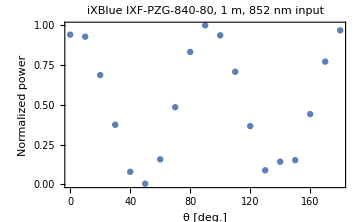

```mathematica
plt=ListPlot[Transpose@{angles,power/Max[power]},FrameLabel->{"θ [deg.]","Normalized power"},PlotLabel->"iXBlue IXF-PZG-840-80, 1 m, 852 nm input"]
```

```mathematica
Export["IXF-PZG-840-80_fiber_1m_constrast_202100806.png",plt]
```

IXF-PZG-840-80_fiber_1m_constrast_202100806.png

```mathematica
max = Max[power];
min = Min[power];
(max-min)/(max+min)
```

0.990999

```mathematica
min/max
```

0.00452083

## Skight polarizers

True

{{-5,1.8093},{4,1.5993},{21,0.6593},{32,0.1053},{40,0.00568},{49,0.1643},{60,0.6923},{61,0.7743},{70,1.2693},{80,1.6693},{85,1.7893},{90,1.6393},{105,1.0093},{115,0.4293},{120,0.2233},{130,0.0037},{133,0.0223},{141,0.2733}}

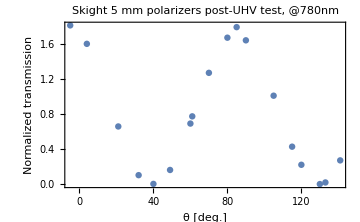

```mathematica
roomlight = 0.0007; (*measured*)
P= {1.81,1.6,0.66,.106,.00638,0.693,0.165,0.775,1.27,1.67,1.64,1.01,.43,0.224,.023,0.274,0.0044,1.79}-roomlight;
θ = {355-360,4,21,32,40,60,49,61,70,80,90,105,115,120,133,141,130,85};
TrueQ[Length[P]==Length[θ]]
data = SortBy[Transpose@{θ,P},#[[1]]&]
plt=ListPlot[data,FrameLabel->{"θ [deg.]","Normalized transmission"},PlotLabel->"Skight 5 mm polarizers post-UHV test, @780nm"]
```

```mathematica
max = Max[P];
min = Min[P];
"contrast"
(max-min)/(max+min)
"min/max"
min/max
```

contrast

0.995918

min/max

0.00204499

-0.00144204

skight_5mm_pol_UHV_test_20211021.png

{{-5,1.81},{4,1.6},{21,0.66},{32,0.106},{40,0.00638},{49,0.165},{60,0.693},{61,0.775},{70,1.27},{80,1.67},{85,1.79},{90,1.64},{105,1.01},{115,0.43},{120,0.224},{130,0.0044},{133,0.023},{141,0.274}}

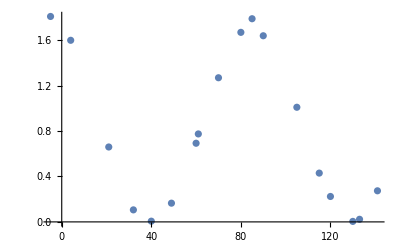

```mathematica
Export["skight_5mm_pol_UHV_test_20211021.png",plt]
```